```mathematica
hito[width_,height_,prob_:1/2]:=Module[{
r=Normalize[Abs@{prob,1-prob}]^2->{0,1},
paths,merge,range,vert,horiz},
If[width>1200/height (* graph is big. skip merging *),
paths=Flatten[#,2]&,
merge=Which[#=={}||#2=={},0,
Last@#==#2[[1]],{{},#~Join~Rest@#2},
#[[1]]==Last@#2,{{},#2~Join~Rest@#},
#[[1]]==#2[[1]],{{},Reverse@#~Join~Rest@#2},
Last@#==Last@#2,{{},Most@#2~Join~Reverse@#},
True,0]&;
paths=Module[{f=Flatten[#,2],q},
Do[
Do[If[ListQ[q=merge@@f[[{i,j}]]],f[[{i,j}]]=q],
{j,2,Length@f},{i,1,j-1}];
If[FreeQ[f,{}],Break[],f=f~DeleteCases~{}],
Length@f];
f]&];
range=If[OddQ[-##],Range[0,#],Range@#-#2]&;
vert=Partition[#+range[height,RandomChoice@r] I,2]&;
horiz=Partition[range[width,RandomChoice@r]+I #,2]&;
paths@{vert/@Range[0,width],horiz/@Range[0,height]}];
```

```mathematica
hitomezashi[x_,y_,csize_:20,prob_:1/2]:=Module[{
r={EdgeForm[Thick],LightYellow,Rectangle[{0,0},{x,y}],Black},
h=hito[x,y,prob],color,t},
Graphics[Join[r,Line/@ReIm@h],ImageSize->x csize]]
```

```mathematica
colorizehito[x_,y_,csize_:20]:=Module[{
h=hitomezashi[x,y,csize,1/2],
img,color,c,r},
img=Rasterize[h];
r=Binarize[Dilation[img,.4],.9];
c=DeleteSmallComponents[DeleteBorderComponents@
MorphologicalComponents[r,CornerNeighbors->False],10];
h=Sort/@Flatten@(ComponentMeasurements[c,"Neighbors"]/.
(a_->b_):>Table[a<->i,{i,b}])//DeleteDuplicates;
h=UndirectedGraph[h,VertexLabels->Automatic];
color=First@ResourceFunction["FindProperColorings"][h,2];
r=Dispatch@MapThread[#1->#2&,{VertexList[h],color}];
ImageMultiply[img,Colorize[c/.r,ColorRules->{0->White,1->LightBlue,2->Pink}]]
]
```

```mathematica
hito[6,3]//Column
```

{3,4,4+ⅈ,5+ⅈ,5,6,6+ⅈ}
{3+2 ⅈ,3+ⅈ,2+ⅈ,2+2 ⅈ,3+2 ⅈ}
{2,1,1+ⅈ,ⅈ,2 ⅈ,1+2 ⅈ,1+3 ⅈ,2+3 ⅈ}
{3+3 ⅈ,4+3 ⅈ,4+2 ⅈ,5+2 ⅈ,5+3 ⅈ,6+3 ⅈ,6+2 ⅈ}

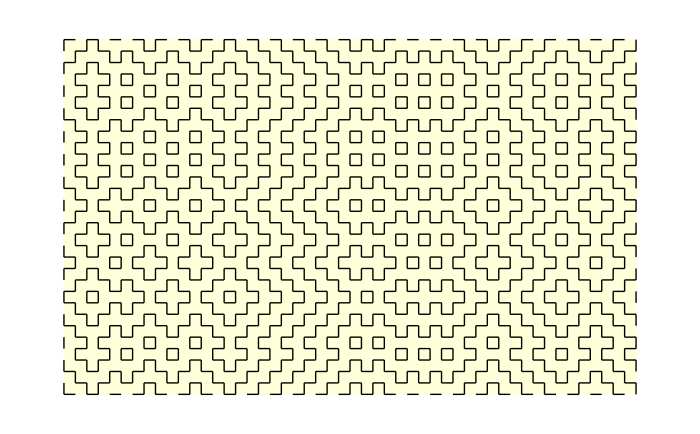

```mathematica
hitomezashi[50,31,14]
```

```mathematica
colorizehito[40,40,15]
```

-Graphics-